```mathematica
deploy
```

CloudObject[]

# Natural gradient for multilayer linear nets

## Util

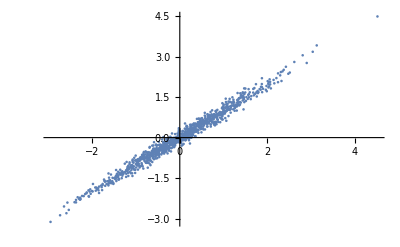

```mathematica
generateXY[e_,yvar_,extraDims_,dsize_]:=Module[{wt,mean,cov,normal,pdf,X,Xc,Y,Xa,wta,w0a,XY,n,trueCov},
SeedRandom[0];
n=2;
wt={{1,1}}; (* true relation *)
mean=0&/@Range@n;
cov={{1, 1-e},{1-e,1}};
normal=MultinormalDistribution[mean,cov];
X=RandomVariate[normal,{dsize}]//Transpose;
X=centerData[X];
Y=Dot[wt, X]+RandomVariate[NormalDistribution[0,√yvar]];
(* Add copies of first feature as redundant features *)
Xa= X~Join~Table[X[[1,All]],{i,extraDims}];
wta=Join[wt,{Table[0,{ i,extraDims}]}, 2];
w0a=Join[{{1,2}},{Table[0,{i,extraDims}]}, 2];
{Xa,Y,w0a}
];
{X0,Y0,w0}=generateXY[0.01,1.,0,1000];
ListPlot[Transpose@X0]
```

## Main

```mathematica
(* Notation:
error is Y-W[n]....W[1].W[0]=Y-W[n].....W[1].X
Wi has size f[i] x f[i-1]
Y has size f[n] x f[-1]
X has size f[0] x f[-1]
fs={f[-1],f[0],f[1],...,f[n]}
 *)


Unprotect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f,flatten,unflatten];
Clear[lossEq,errEq,gradEq,hessEq,n,dsize,W,U,makeW,Y,X,vars,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];

Clear[A,B,dW,W,X,Y,y,x,fs, subW,loss,err];
(* Ws gives list of matrices, Wf means flattened representation *)
(* Wf gives list of symbolic variables, W0f gives concrete values *)

On[Assert];
SeedRandom[0];
fs={10,2,2,2,1} ;
dsize=First[fs];
(* number of layers aka number of matmuls *)
n=Length[fs]-2;

dsize=First@fs;
(* makeW[0] is X *)
makeW[k_]:=Array[W[k],{fs[[k+2]],fs[[k+1]]}];
makeInitializer[k_]:=RandomReal[{0,1},{fs[[k+2]],fs[[k+1]]}];

vars=Table[makeW[k],{k,1,n}];
Ws=vars;
varsf=Flatten[vec/@vars];
Wf=varsf;
W0=Table[makeInitializer[k],{k,1,n}];
(* W true flat *)
Wtf={0.8062349520611257,0.8058281619635977,0.8373291816030192,0.7906864569952768,1.1965576018047888,0.30483187178626686,1.2476949293612638,0.8154112123212373,0.12928385363990855,0.8254921329944452};
(* W0 flat *)
W0f=Flatten[vec/@W0];
(* Y-Wn....W1.W0 *)
errEq:=Y-Fold[Dot,Reverse@vars].makeW[0];
lossEq:=take1[1/(2 dsize)errEq.errEqᵀ];

subW[Wf_]:=Thread[varsf->Wf];

X=Array[W[0],{fs[[2]],fs[[1]]}];
X0=RandomReal[{0,1},{fs[[2]],fs[[1]]}];
subX:=(
Assert[Dimensions[X0]=={fs[[2]],fs[[1]]},"X mismatch"];Thread[Flatten@X->Flatten@X0]
);

Y=Array[y,{fs[[-1]],fs[[1]]}];
Y0=RandomReal[{0,1},{fs[[-1]],fs[[1]]}];
subY:=(
Assert[Dimensions[Y0]=={Last[fs], First[fs]},"Y mismatch"];
Thread[Flatten@Y->Flatten@Y0]
);

{X0,Y0,dummy}=generateXY[0.01,1.,0,First@fs];

flatten[Ws_]:=c2v[vec/@Ws];
unflatten[Wf_]:=Module[{},
sizes=Rest[Times@@#&/@Partition[fs,2,1]];
flatVars=listPartition[Wf,sizes];
Table[unvec[flatVars[[i]],fs[[i+2]]],{i,1,Length@sizes}]
];

(* Define loss, gradient, Hessian *)
lossf[Wf_]:=(lossEq/.subW[Wf]/.subY/.subX);
loss[Ws_]:=lossf[flatten[Ws]];

Assert[vars==unflatten[varsf],"vars mismatch"];

gradEq=D[lossf[Wf],{Wf,1}];
hessEq=D[lossf[Wf],{Wf,2}];
gradf[Wf_]:=gradEq/.subW[Wf];
hessf[Wf_]:=hessEq/.subW[Wf];
ihessf[Wf_]:=PseudoInverse[hessf[Wf]];

(* Manual implementation of gradient *)

(* A[i]=W[i-1]...W[0] = fprop needed to compute derivative at layer i *)
A[Wf_,1]:=makeW[0]/.subX;
A[Wf_,i_]:=Module[{},
makeW[i-1].A[Wf,i-1]/.subW[Wf]
];

(* B[i]=W[i+1]'...err = bprop needed to compute derivative at layer i *)
err[Ws_]:=Y-A[flatten@Ws,n+1]/.subY;
B[Wf_,n]:=err[unflatten[Wf]];
B[Wf_,i_]:=Module[{},
makeW[i+1]ᵀ.B[Wf,i+1]/.subW[Wf]
];

dW[Wf_,i_]:=-B[Wf,i].A[Wf,i]ᵀ/dsize;

Assert[gradf[W0f]==flatten[dW[W0f,#]&/@Range[n]], "Gradient incorrect"];
Protect[lossEq,errEq,gradEq,hessEq,errF,lossF,gradF,hessF,pre0,n,dsize,W,U,makeW,Y,X,vars,Wf,allvars,A,B,Bn,hessBlock,hess,gradBlock,grad,sub1,subr,y,f];
```

## Newton Method

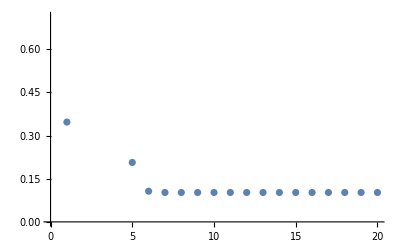

```mathematica
Clear[pointList,gradList,preList,lossList];
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizeNewton[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf].ihessf[wf]
];
];
optimizeNewton[1.,W0f,20];
(*Export["~/git/whitening/exp/data/natural_gradient_multilayer_losses_newton.csv",lossList];*)
ListPlot[lossList]
```

```mathematica
Export["~/git/whitening/exp/data/natural_gradient_multilayer_hess0.csv",(D[lossf[Wf],{Wf,2}])/.subW[W0f]]
```

~/git/whitening/exp/data/natural_gradient_multilayer_hess0.csv

## Natural Gradient Method

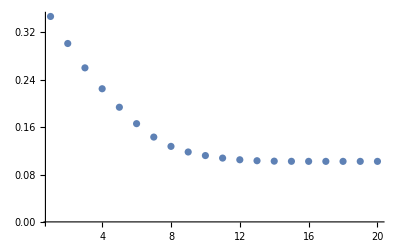

```mathematica
(* get single X *)
makeX1[i_]:=v2c[Table[W[0][j,i],{j,fs[[2]]}]];
Assert[Join@@(Table[makeX1[i],{i,10}]~Join~{2})==makeW[0]];

makeY1[i_]:=Y[[All,i]];errEq1[i_]:=makeY1[i]-Fold[Dot,Reverse@vars].makeX1[i];
lossEq1[i_]:=(take1[1/(2 dsize)errEq1[i].errEq1[i]ᵀ]);
lossf1[Wf_,i_]:=(lossEq1[i]/.subW[Wf]/.subY/.subX);
gradEq1[i_]:=D[lossf1[Wf,i],{Wf,1}];
gradf1[Wf_,i_]:=gradEq1[i]/.subW[Wf];

Assert[v2c[-B[W0f,1][[All,1]]].{ A[W0f,1][[All,1]]}/dsize==First[unflatten[gradf1[W0f,1]]], "gradient incorrect"]

fisher[Wf_]:=Module[{},
(* dsize x fsize *)
gradList=Table[gradf1[Wf,i],{i,First[fs]}];
gradListᵀ.gradList/dsize
];

ifisher[Wf_]:=PseudoInverse[fisher[Wf]];

optimizeNatural[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList,temp}={{},{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~{{gradf[wf]}};
temp=temp~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf].ifisher[wf]
];
];
optimizeNatural[.001,W0f,20];
Export["~/git/whitening/exp/data/natural_gradient_multilayer_losses_fisher.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

### Examine off-diagonal correlations

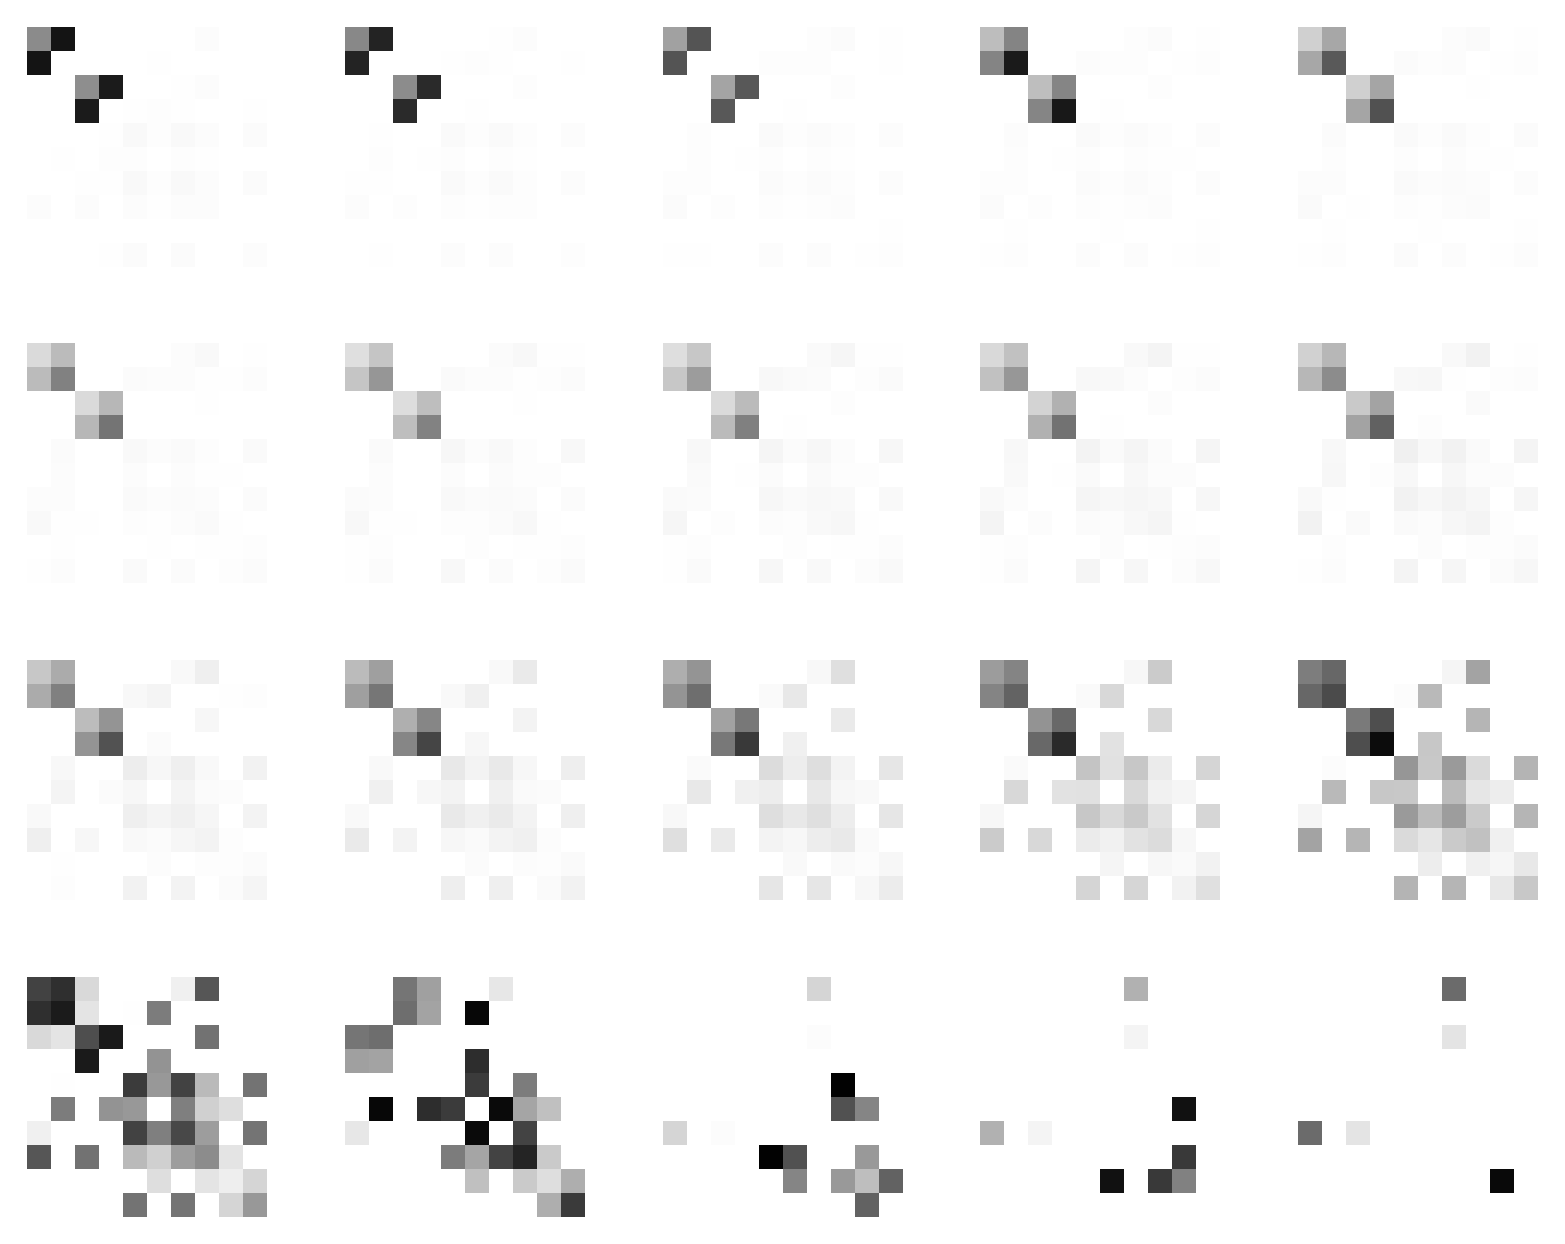

```mathematica
plots=ArrayPlot[#,PlotRange->{0,100}]&/@preList;
GraphicsGrid[Partition[plots,5]]
```

### Plot weight magnitudes in two layers

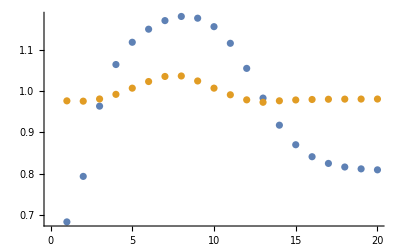

```mathematica
layer1sizes=magnitudeVec[1,#]&/@pointList;
layer2sizes=magnitudeVec[2,#]&/@pointList;
ListPlot[{layer1sizes,layer2sizes}]
```

### Plot update per layer

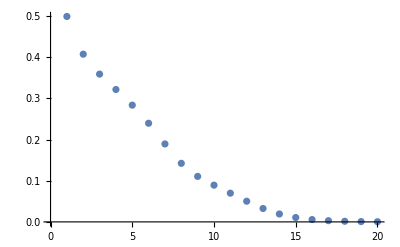

```mathematica
updates1=Table[vectorBlock[1,temp[[i]]].matrixBlock[1, 1, preList[[i]]].vectorBlock[1,temp[[i]]],{i,20}];
updates2=Table[vectorBlock[2,temp[[i]]].matrixBlock[2, 2, preList[[i]]].vectorBlock[2,temp[[i]]],{i,20}];
updates3=Table[vectorBlock[3,temp[[i]]].matrixBlock[3, 3, preList[[i]]].vectorBlock[3,temp[[i]]],{i,20}];


ListPlot[{updates1}]
```

```mathematica
ListPlot[{updates2}]
```

-Graphics-

## Gradient descent

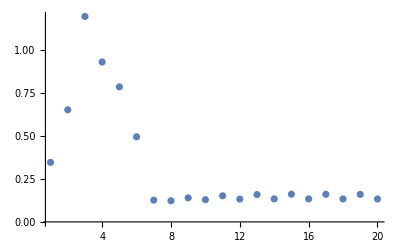

```mathematica
optimizeRegular[lr_,w0f_,iters_]:=Module[{wf},
{pointList, gradList,preList, lossList}={{},{},{},{}};
wf=w0f;
For[iter=1,iter≤iters,iter++,
pointList=pointList~Append~wf;
gradList=gradList~Append~gradf[wf];
preList=preList~Append~ihessf[wf];
lossList=lossList~Append~lossf[wf];
wf=wf-lr*gradf[wf]
];
];
optimizeRegular[.5,W0f,20];
(*Export["~/git/whitening/exp/data/natural_gradient_multilayer_losses_regular.csv",lossList];*)
Export["~/git/whitening/exp/data/natural_gradient_multilayer_losses_gd.csv",lossList];
ListPlot[lossList,PlotRange->All]
```

## Generate data for TF

```mathematica
Export["~/git/whitening/exp/data/natural_gradient_multilayer_W0f.csv",W0f];
Export["~/git/whitening/exp/data/natural_gradient_multilayer_XY0.csv",X0~Join~Y0];Export["~/git/whitening/exp/data/natural_gradient_multilayer_fs.csv",fs];
Export["~/git/whitening/exp/data/natural_gradient_multilayer_loss0.csv",lossf[W0f]];
```

```mathematica
Export["~/git/whitening/exp/data/natural_gradient_multilayer_fisher0.csv",fisher[W0f]];
```

```mathematica
Export["~/git/whitening/exp/data/natural_gradient_multilayer_fisher0.csv",fisher[W0f]];
```

## Khatri Rao comparison

```mathematica
khatriRao[A_,B_]:=MapThread[Flatten[{#1}⊗{#2}]&,Transpose/@{A,B}]//Transpose;
vecs[n_,dsize_]:=(
SeedRandom[0];
A=RandomReal[{0,1},{n,dsize}];
(*B=RandomReal[{0,1},{n,dsize}];*)
cov1 = A.Aᵀ/dsize;
cov2=khatriRao[A,A].khatriRao[A,A]ᵀ/dsize;
eigs1=Eigenvalues[cov1];
eigs2=Eigenvalues[cov2];
)
```

```mathematica
countEigs[k_]:=(
vecs[k,1000];
c1=Count[#>0&/@Chop@eigs1,True];
c2=Count[#>0&/@Chop@eigs2,True];
{c1,c2}
)
```

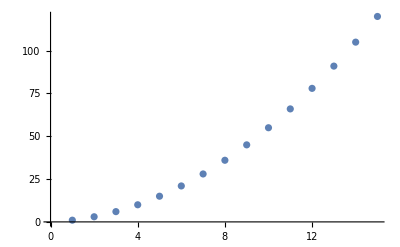

```mathematica
points=countEigs[#]&/@Range[15];
ListPlot[points]
```

```mathematica
points
```

{{1,1},{2,3},{3,6},{4,10},{5,15},{6,21},{7,28},{8,36},{9,45},{10,55},{11,66},{12,78},{13,91},{14,105},{15,120}}